```mathematica
makeninesquares[{v1_, v2_}]:= Module[{},
l = Norm[(v1-v2)];
Subscript[e, 1] = l/(3 √2){1,0};
Subscript[e, 2] = l/(3 √2){0,1};
lower[i_,j_]:= v1 + i Subscript[e, 1]+j Subscript[e, 2];
upper[i_,j_]:= lower[i,j] + Subscript[e, 1] + Subscript[e, 2];
lowerlist =Flatten[Table[{lower[i,j],upper[i,j]},{i, 0, 2},{j,0,2}],1];
Delete[lowerlist,5]
]
```

```mathematica
makeninesquares[{{0,0},{1,1}}]
drawrectangles[{p_,q_}] := Rectangle[p,q]
```

{{{0,0},{1/3,1/3}},{{0,1/3},{1/3,2/3}},{{0,2/3},{1/3,1}},{{1/3,0},{2/3,1/3}},{{1/3,1/3},{2/3,2/3}},{{1/3,2/3},{2/3,1}},{{2/3,0},{1,1/3}},{{2/3,1/3},{1,2/3}},{{2/3,2/3},{1,1}}}

```mathematica
s1={{0.,0.},{1.,1.}}
```

{{0.,0.},{1.,1.}}

```mathematica
sier2[list_]:=Flatten[Map[makeninesquares, list],1]
```

```mathematica
sier3[n_,list_]:= Nest[sier2, list,n]
```

```mathematica
sier3[2,{s1}];
sier4[n_,list_]:=Graphics[Map[drawrectangles,sier3[n,list]],ImageSize->900]
```

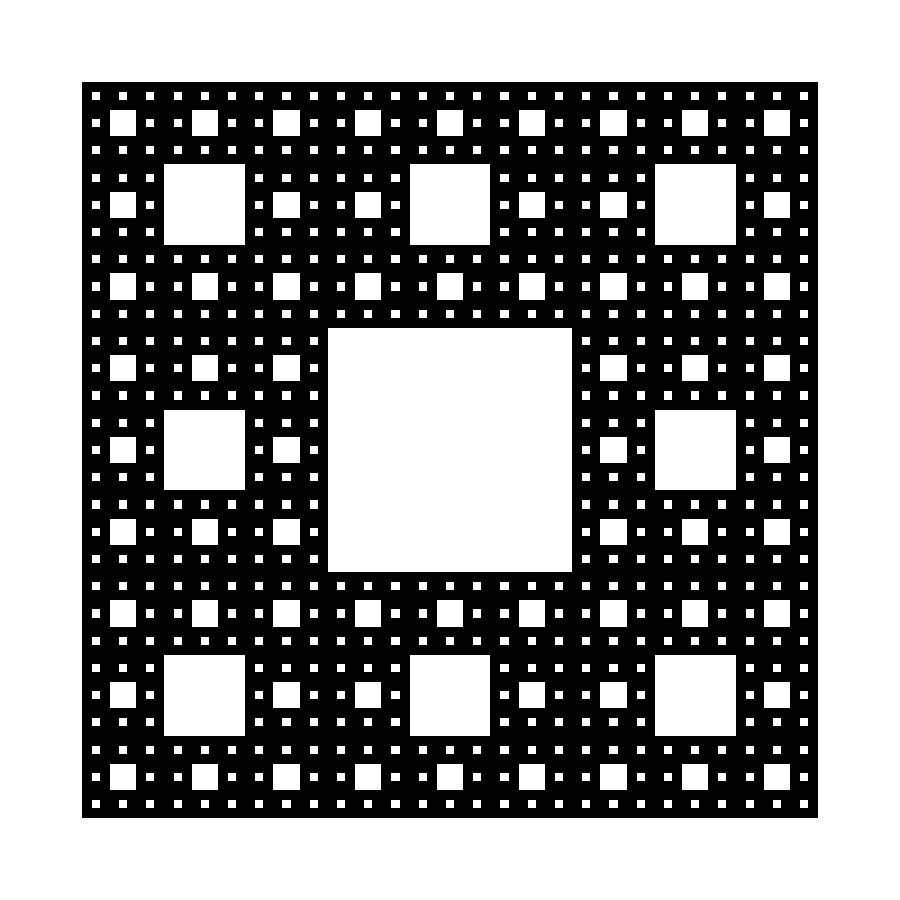

```mathematica
sier4[4,{s1}]
```